```mathematica
filename="E:\\Cavendish\\runs\\run4.MOV";
frames=Import[filename,"ImageList"];
```

```mathematica
Manipulate[ImageTake[frames[[1]],{a,b},{c,d}],{a,1,1080},{b,2,1080},{c,1,1920},{d,2,1920}]
```

```mathematica
length=Length[frames];
ymin=240;
ymax=360;
xmin=1;
xmax=1920;
croppedFrames=Table[ImageTake[frames[[i]],{ymin,ymax},{xmin,xmax}],{i,length}];
```

```mathematica
croppedFrames[[1]]
imgDim=ImageDimensions[croppedFrames[[1]]]
```

-Graphics-

{1920,121}

```mathematica
binarizedFrames=Table[Binarize[croppedFrames[[i]],.5],{i,length}];
newBinarizedFrames=Table[DeleteSmallComponents[binarizedFrames[[i]]],{i,length}];
```

```mathematica
help=Table[ComponentMeasurements[newBinarizedFrames[[i]],"Centroid"],{i,length}]//Values;
xvals=Flatten[help[[;;,;;,1]]];
yvals=Flatten[help[[;;,;;,2]]];
```

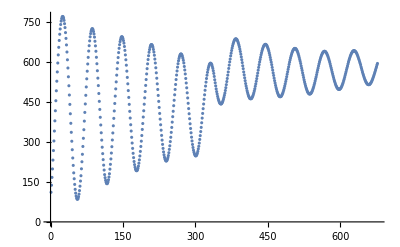

{111.,137.5,166.833,198.5,231.667,267.3,303.3,340.5,378.7,416.5,454.071,491.357,527.3,562.,595.452,625.8,654.214,679.944,703.214,723.,739.7,752.5,761.682,767.929,769.929,768.864,763.833,755.3,742.875,728.214,709.375,687.7,663.214,636.7,607.5,576.786,543.833,510.214,475.5,440.375,405.3,369.5,335.7,302.3,270.5,239.5,211.7,183.773,161.667,140.5,122.,107.833,97.,89.3333,85.3,84.8333,87.1667,94.3,104.,117.3,133.833,153.,173.,199.,225.357,253.333,282.7,313.3,345.5,377.7,410.3,442.,474.389,505.7,536.167,564.786,591.8,616.577,640.333,660.375,678.357,693.667,705.7,714.5,720.5,724.,723.929,720.5,713.5,704.357,692.5,677.,659.7,639.5,616.864,592.722,566.5,538.786,510.833,481.214,451.786,421.5,392.,363.167,334.,306.5,279.9,255.833,233.3,212.7,194.3,177.167,165.833,156.,148.833,143.9,143.,145.,149.833,157.833,168.167,180.429,197.7,215.75,235.9,258.,281.833,306.9,333.3,360.167,388.,415.7,443.833,471.375,498.5,524.667,550.,573.9,596.333,615.9,634.5,650.5,664.167,675.7,683.667,690.7,693.667,693.9,691.833,687.3,679.5,669.929,657.3,642.786,625.8,607.553,587.3,565.,541.5,517.5,492.125,466.5,440.5,414.3,389.214,364.167,340.5,317.,295.5,275.5,257.,240.833,226.3,214.7,204.9,197.7,193.167,191.833,192.167,195.,200.9,209.1,220.,232.5,247.083,264.167,282.7,302.5,323.7,346.5,368.7,393.,416.5,441.,465.,488.5,511.5,533.5,554.5,574.333,592.31,608.5,622.833,635.682,645.75,654.125,660.333,663.5,664.786,663.667,660.5,654.929,646.357,636.625,624.611,610.147,595.409,577.625,558.667,538.5,517.375,496.357,473.944,451.7,428.875,406.5,385.167,364.,343.7,324.167,306.5,290.5,275.5,262.3,251.5,242.25,235.5,231.,228.5,228.167,230.167,234.333,240.833,248.667,259.333,271.833,285.167,301.,317.167,335.5,354.,373.9,394.3,414.5,435.5,455.75,476.3,496.357,515.,533.5,550.333,565.667,579.929,592.778,603.816,612.583,619.611,625.,628.136,629.5,628.5,625.8,620.9,613.654,605.6,595.636,582.5,569.3,554.375,537.5,520.5,502.5,483.7,464.5,444.5,424.7,405.333,386.75,367.7,350.,334.,317.5,303.333,290.214,278.833,268.833,260.9,254.833,250.5,247.833,247.375,248.667,252.333,257.3,264.5,273.667,283.3,295.3,309.,323.3,338.5,354.167,371.5,389.,406.5,424.333,441.7,459.5,476.3,493.3,509.,523.7,537.357,549.667,560.5,570.75,578.5,585.,590.063,593.119,594.85,594.184,592.25,589.083,582.375,575.357,566.5,556.5,545.125,532.7,521.3,509.7,498.357,488.3,479.5,470.357,462.625,456.375,451.,446.5,444.,442.375,442.,442.643,445.375,448.375,453.5,459.5,466.5,474.3,482.5,492.5,503.,514.3,526.,537.5,549.9,561.929,575.167,587.5,599.548,610.265,622.167,632.167,642.375,651.2,659.5,666.625,672.5,677.9,681.625,684.214,685.786,685.929,685.,683.3,679.625,675.214,669.625,663.167,656.389,647.389,638.625,628.625,618.375,607.864,596.976,585.056,574.167,561.929,551.125,540.,529.3,518.5,509.3,500.5,491.786,484.667,477.875,472.214,468.3,464.5,462.3,461.5,461.5,462.3,464.5,468.3,472.214,477.643,484.1,491.214,499.,508.071,517.167,526.833,537.,547.3,557.5,568.5,579.,589.438,599.405,608.556,617.136,626.375,633.944,641.5,647.625,652.944,657.5,661.071,663.25,664.75,665.625,664.625,663.1,660.75,656.5,651.625,646.625,640.375,633.,625.,616.333,607.611,598.636,589.286,579.,568.75,558.375,548.9,538.75,529.333,520.375,511.5,503.5,496.5,489.375,484.333,479.5,475.,472.,470.333,469.167,469.167,470.1,471.333,475.,478.75,483.,488.7,495.,501.7,509.5,517.5,526.214,534.5,544.,553.214,562.389,571.667,580.667,590.132,598.738,606.864,614.5,621.375,627.611,633.833,638.5,642.625,645.625,648.,649.625,650.375,649.643,648.9,646.333,643.389,639.625,634.833,629.375,623.,616.3,608.667,601.595,593.5,584.5,575.9,567.7,558.375,549.9,541.375,532.7,524.7,517.5,510.375,503.7,498.357,493.,488.3,485.,482.611,480.214,479.5,479.5,479.833,481.,484.,486.75,490.7,496.,501.214,507.125,514.,520.7,528.5,536.3,543.5,552.,560.375,568.5,576.125,584.5,592.342,599.69,606.333,612.7,618.5,623.75,627.8,631.864,634.833,637.214,638.5,639.5,639.25,638.5,636.5,633.8,631.227,626.643,622.5,617.167,611.5,605.5,599.35,592.35,584.611,577.643,570.333,562.625,555.375,548.167,541.214,533.9,527.833,522.375,516.5,511.5,507.786,503.5,501.214,498.5,497.5,496.5,496.5,497.5,499.,501.214,504.167,508.071,512.5,517.5,522.357,529.,534.75,541.667,548.9,556.,563.,570.833,577.625,584.375,592.045,599.2,605.667,611.433,616.808,622.625,626.5,631.227,633.944,637.375,639.5,641.167,641.3,641.389,641.,639.071,637.375,634.6,631.417,627.167,622.625,617.5,612.071,607.022,600.804,594.778,588.955,581.357,574.9,568.,561.375,555.125,549.5,543.667,538.167,533.3,529.1,524.833,521.833,518.833,516.5,515.25,514.5,514.333,514.625,515.643,517.625,520.167,522.833,526.5,530.786,535.3,540.5,545.5,551.125,556.929,562.833,569.,575.357,581.357,588.4,593.816}

E:\Cavendish\runs\run4data.csv

```mathematica
ListPlot[Transpose[xvals]]

dataset = Transpose[xvals]
Export["E:\\Cavendish\\runs\\run4data.csv",dataset,"CSV"]
```